```mathematica
(*Tarea 1*)
NPuntos = 1000; 
X0 = 0; 
Xf = 2*Pi;
DeltaX = (Xf-X0)/(NPuntos-1);
Fun[i_] := X0+DeltaX*i;  
X = Array[Fun, NPuntos,0];
A = X +0.5;
B = 0.5*Cos[X];
CC = X*X + 0.5;
f = Cos[2*X];
Arriba = A + DeltaX*B/2;
Abajo = A - DeltaX*B/2;
Diag = DeltaX*DeltaX*CC-2*A;
(* Condiciones iniciales *)
F =f;
F[[1]] = f[[1]] - A[[1]]/(DeltaX*DeltaX) - B[[1]]/(2*DeltaX);
(* Condiciones iniciales *)
F[[NPuntos]] = f[[NPuntos]]  - A[[NPuntos]]/(DeltaX*DeltaX) - B[[NPuntos]]/(2*DeltaX);
MatrixA =(SparseArray[{Band[{2,1}]->Abajo[[2;;NPuntos]], Band[{1,1}]->Diag,Band[{1,2}]->Arriba[[1;;NPuntos-1]] },{NPuntos,NPuntos}])/(DeltaX*DeltaX);
MatrixA[[1;;1,1;;3]];
MatrixA[[1;;1,NPuntos-2;;NPuntos]];
Solucion = LinearSolve[MatrixA, F];
```

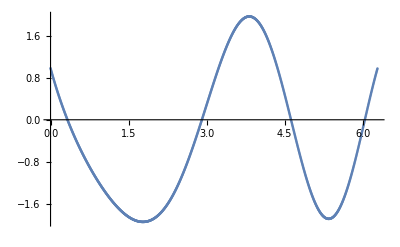

```mathematica
data=Transpose@{X,Solucion};
ListPlot[data]
```

```mathematica
(*Tarea 2: Péndulo no lineal*)
```

```mathematica
G = ConstantArray[0,NPuntos] ;
J = ConstantArray[0,{NPuntos, NPuntos}];
delta =  ConstantArray[0,NPuntos] ;
```

```mathematica
Norm[J]
```

0

```mathematica
While[Norm[delta]>E-8, 
G = (1/(DeltaX*DeltaX))*()
]
```

```mathematica
.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10.10
```